## Robust Regression

https://en.wikipedia.org/wiki/Huber_loss

https://mathematica.stackexchange.com/questions/224980/how-to-drop-points-that-dont-lie-in-a-line

```mathematica
data={{311.,191.},{324.5,374.5},{357.,436.5},{328.,730.5},{333.,1196.},{334.,1552.},{344.,1827.5}};
```

```mathematica
abponts=FindAnomalies[data]
```

{{357.,436.5}}

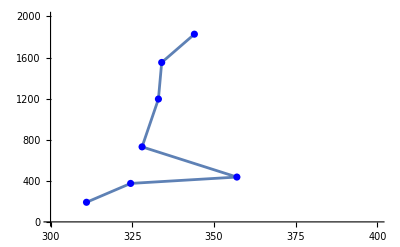

```mathematica
Show[ListLinePlot[SortBy[data,Last],PlotRange->{{300,400},{0,2000}}],ListPlot[data,PlotStyle->Blue]]
```

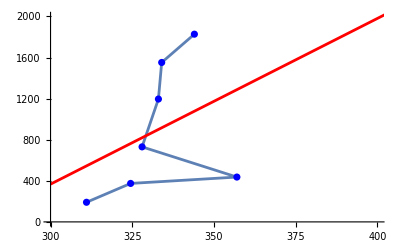

```mathematica
Show[ListLinePlot[SortBy[data,Last],PlotRange->{{300,400},{0,2000}}],Plot[Evaluate[Fit[data,{1,x},x]],{x,300,500},PlotStyle->Red],ListPlot[data,PlotStyle->Blue]]
```

```mathematica
sol0=FindFit[data,a+b x,{a,b},x]
```

{a→-4473.5,b→16.1366}

```mathematica
sol1=FindFit[data,a+b x,{a,b},x,NormFunction->{"HuberPenalty",1}]
```

{a→-14003.9,b→45.6426}

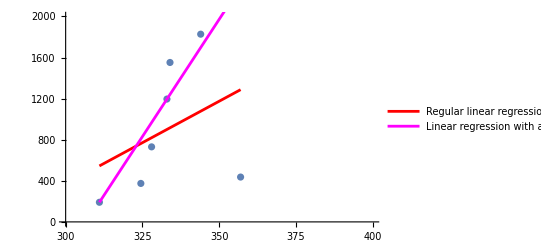

```mathematica
Show[ListPlot[SortBy[data,Last],PlotRange->{{300,400},{0,2000}}],Plot[{a+b x/. sol0,a+b x/. sol1},{x,Min[data[[All,1]]],Max[data[[All,1]]]},PlotLegends->{"Regular linear regression","Linear regression with a Huber penalty"},PlotStyle->{Red,Magenta}]]
```

```mathematica
data
```

{{311.,191.},{324.5,374.5},{357.,436.5},{328.,730.5},{333.,1196.},{334.,1552.},{344.,1827.5}}

```mathematica
residuos=Table[(data[[k,2]]-(a+b data[[k,1]])/.sol0),{k,Length@data}]
```

{-353.985,-388.329,-850.769,-88.8072,296.01,635.873,750.007}

```mathematica
huber[a_,δ_]:=Piecewise[{{(1/2)a^2,Abs[a]<=δ},{δ(Abs[a]-(1/2) δ),Abs[a]>δ}}]
```

```mathematica
hubdata=huber[#,380]&/@ residuos
```

{62652.6,75365.1,251092.,3943.36,43810.9,169432.,212803.}

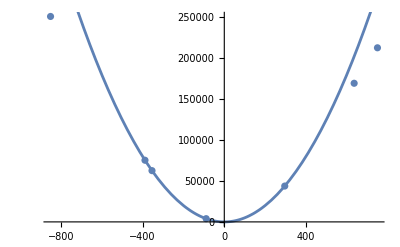

```mathematica
Show[ListPlot[{residuos,hubdata}ᵀ],Plot[(1/2) x^2,{x,-750,750}]]
```

```mathematica
Manipulate[Show[ListPlot[{residuos,huber[#,thre]&/@ residuos}ᵀ],Plot[(1/2) x^2,{x,-750,750}]],{{thre,500},1,1000,10}]
```

```mathematica
residuos2=Table[(data[[k,2]]-(a+b data[[k,1]])/.sol1),{k,Length@data}]
```

{0.0681818,-432.606,-1853.99,-236.355,0.931818,311.289,130.364}

```mathematica
Manipulate[Show[ListPlot[{residuos2,huber[#,thre]&/@ residuos2}ᵀ],Plot[(1/2) x^2,{x,-750,750},PlotRange->All],PlotRange->All],{{thre,500},1,1000,10}]
```

```mathematica
buscadelta[datos_,δ_]:=Module[{},
soldelta=FindFit[datos,a+b x,{a,b},x,NormFunction->{"HuberPenalty",δ},AccuracyGoal->10,PrecisionGoal->10];
mincuad=Sum[(datos[[k,2]]-(a+b datos[[k,1]])^2/.soldelta),{k,Length@datos}];
{δ,mincuad}];
```

```mathematica
huberdelta=Table[buscadelta[data,δ],{δ,100,1000,10}]//Quiet;
```

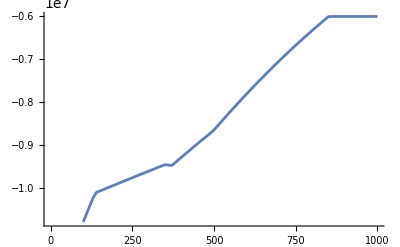

```mathematica
ListLinePlot[huberdelta]
```

```mathematica
huberdelta=Table[buscadelta[data,δ],{δ,360,380,1}]//Quiet;
```

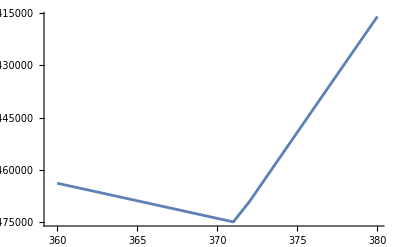

```mathematica
ListLinePlot[huberdelta]
```

## Jackknife

https://es.wikipedia.org/wiki/Jackknife_(estadística)

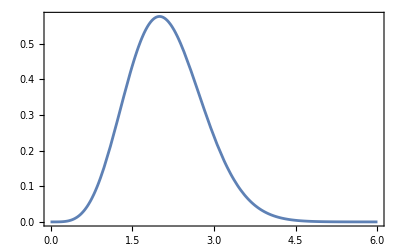

```mathematica
Plot[PDF[ChiDistribution[5],x],{x,0,6},Frame->True]
```

```mathematica
datos=RandomVariate[ChiDistribution[5],100];
```

```mathematica
datos
```

{2.91655,2.80746,2.00955,0.843998,2.7581,1.68742,2.78689,1.72304,3.61754,3.35751,1.69858,2.98734,2.17683,2.01371,2.48699,2.44615,3.10564,2.40988,2.65634,2.39997,1.38804,3.1845,1.19431,2.0831,1.14382,2.05111,2.50888,1.5259,2.82283,2.30129,1.86794,1.88173,0.905203,2.72832,3.17276,2.93656,2.31224,2.19752,1.47268,1.26131,2.4096,2.95441,2.0743,2.42158,1.63836,1.4975,1.7435,2.25748,1.23537,1.45566,3.95493,1.76847,1.43629,3.35079,2.64357,1.7516,2.017,2.5702,3.18565,1.96123,2.58242,1.1789,1.52569,1.18872,2.53647,3.26309,1.73517,3.21531,1.12982,1.96188,1.50767,1.77852,2.06577,1.75844,2.32242,2.76973,2.31849,1.92063,1.86478,1.61317,2.75056,1.5532,1.60365,1.55068,1.9143,1.22019,2.11739,1.61998,2.80735,1.78584,1.95852,2.11051,2.00693,2.36735,2.26765,1.75389,2.47762,3.39159,1.07545,4.019}

```mathematica
Drop[datos,{1}]
```

{2.80746,2.00955,0.843998,2.7581,1.68742,2.78689,1.72304,3.61754,3.35751,1.69858,2.98734,2.17683,2.01371,2.48699,2.44615,3.10564,2.40988,2.65634,2.39997,1.38804,3.1845,1.19431,2.0831,1.14382,2.05111,2.50888,1.5259,2.82283,2.30129,1.86794,1.88173,0.905203,2.72832,3.17276,2.93656,2.31224,2.19752,1.47268,1.26131,2.4096,2.95441,2.0743,2.42158,1.63836,1.4975,1.7435,2.25748,1.23537,1.45566,3.95493,1.76847,1.43629,3.35079,2.64357,1.7516,2.017,2.5702,3.18565,1.96123,2.58242,1.1789,1.52569,1.18872,2.53647,3.26309,1.73517,3.21531,1.12982,1.96188,1.50767,1.77852,2.06577,1.75844,2.32242,2.76973,2.31849,1.92063,1.86478,1.61317,2.75056,1.5532,1.60365,1.55068,1.9143,1.22019,2.11739,1.61998,2.80735,1.78584,1.95852,2.11051,2.00693,2.36735,2.26765,1.75389,2.47762,3.39159,1.07545,4.019}

```mathematica
jacdat=Table[Drop[datos,{k}],{k,Length@datos}];
```

```mathematica
Dimensions@jacdat
```

{100,99}

```mathematica
AbsoluteTiming[solsk=FindMaximum[LogLikelihood[ChiDistribution[ν],#],{ν}]& /@ jacdat;//Quiet]
```

{0.078557,Null}

```mathematica
nues=ν/.solsk[[All,2]]
```

{5.16436,5.16762,5.19638,5.2719,5.16914,5.21149,5.16825,5.20968,5.14594,5.15231,5.21091,5.1623,5.18949,5.1962,5.17803,5.17945,5.15898,5.18073,5.17237,5.18109,5.22843,5.15683,5.24152,5.19328,5.24529,5.19462,5.17727,5.22021,5.16715,5.1847,5.20269,5.20206,5.26575,5.17007,5.15715,5.16377,5.18429,5.18867,5.22329,5.23676,5.18074,5.16325,5.19365,5.18032,5.21404,5.22184,5.20865,5.18635,5.23857,5.2243,5.13835,5.20742,5.22546,5.15248,5.17278,5.20825,5.19606,5.1752,5.1568,5.19848,5.17479,5.24265,5.22022,5.24193,5.17633,5.15475,5.20907,5.15601,5.24636,5.19845,5.22125,5.20693,5.194,5.20792,5.18391,5.16878,5.18406,5.20029,5.20284,5.21538,5.16938,5.21867,5.2159,5.21881,5.20057,5.23965,5.19187,5.21502,5.16763,5.20658,5.1986,5.19215,5.19649,5.18226,5.18597,5.20814,5.17835,5.15145,5.25067,5.13698}

```mathematica
promν=Mean[nues]
```

5.19445

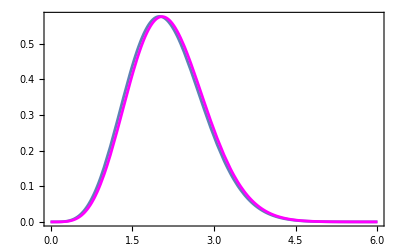

```mathematica
Show[Plot[PDF[ChiDistribution[5],x],{x,0,6},Frame->True],Plot[PDF[ChiDistribution[promν],x],{x,0,6},Frame->True,PlotStyle->Magenta]]
```

```mathematica
StandardDeviation[nues]
```

0.0285646

```mathematica
Quantile[nues,{0.025,0.975}]
```

{5.14594,5.25067}

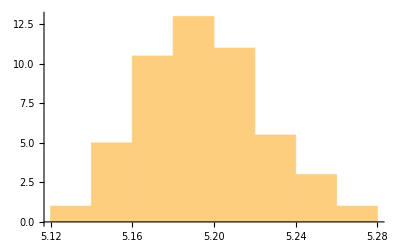

```mathematica
Histogram[nues,Automatic,"PDF"]
```

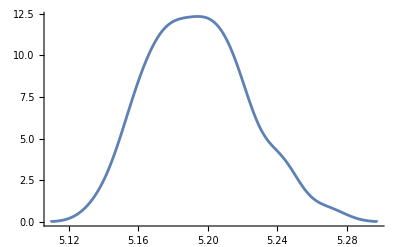

```mathematica
SmoothHistogram[nues,PlotRange->All]
```

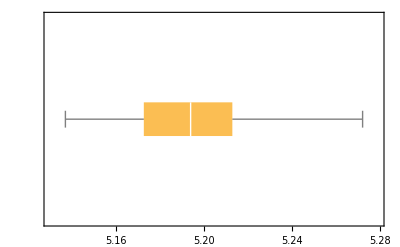

```mathematica
BoxWhiskerChart[nues,BarOrigin->Left]
```

## Ejemplo JackKnife

datos del seeing

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/michel/Library/CloudStorage/OneDrive-uv.cl/cursos/pregrado/Estadisticas/2024/Clases

```mathematica
seeingOrig=Rest@Import["dimm_17_18.csv"][[All,2]]
```

```mathematica
seeing=RandomChoice[seeingOrig,100];
```

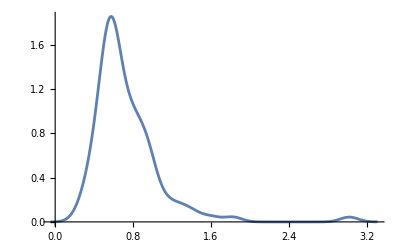

```mathematica
SmoothHistogram@seeing
```

```mathematica
Length@seeing
```

100

```mathematica
Select[seeing,NumberQ]//Length
```

100

```mathematica
FindDistribution[seeing,TargetFunctions->{NormalDistribution}]
```

MixtureDistribution[{0.8916,0.1084},{NormalDistribution[0.656374,0.202074],NormalDistribution[1.55943,0.769839]}]

```mathematica
modelo=MixtureDistribution[{a1,a2},{NormalDistribution[μ1,σ1],NormalDistribution[μ2,σ2]}]
```

MixtureDistribution[{a1,a2},{NormalDistribution[μ1,σ1],NormalDistribution[μ2,σ2]}]

```mathematica
llk=LogLikelihood[modelo,seeing];
```

```mathematica
sol=NMaximize[{llk,a1>0,a2>0,σ1>0,σ2>0},{{a1,0.1,0.9},{a2,0.1,0.9},{μ1,.5,.9},{σ1,.1,.3},{μ2,1.,2.},{σ2,.5,1.5}}]
```

$Aborted

```mathematica
AbsoluteTiming[sol=FindMaximum[Re@llk,{{a1,0.8},{a2,0.2},{μ1,.67},{σ1,.18},{μ2,1.3},{σ2,.5}}]]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.026451,{-10.4713,{a1→0.821608,a2→0.114338,μ1→0.653504,σ1→0.191082,μ2→1.3342,σ2→0.620572}}}

```mathematica
jacdat=Table[Drop[seeing,{k}],{k,Length@seeing}];
```

```mathematica
Dimensions@jacdat
```

{100,99}

```mathematica
AbsoluteTiming[solsk=FindMaximum[Re@LogLikelihood[modelo,#],{{a1,0.8},{a2,0.2},{μ1,.67},{σ1,.18},{μ2,1.3},{σ2,.5}}]& /@ jacdat;//Quiet]
```

{1.33924,Null}

```mathematica
μes1=μ1/.solsk[[All,2]];
μes2=μ2/.solsk[[All,2]];
σes1=σ1/.solsk[[All,2]];
σes2=σ2/.solsk[[All,2]];
aes1=a1/.solsk[[All,2]];
aes2=a2/.solsk[[All,2]];
```

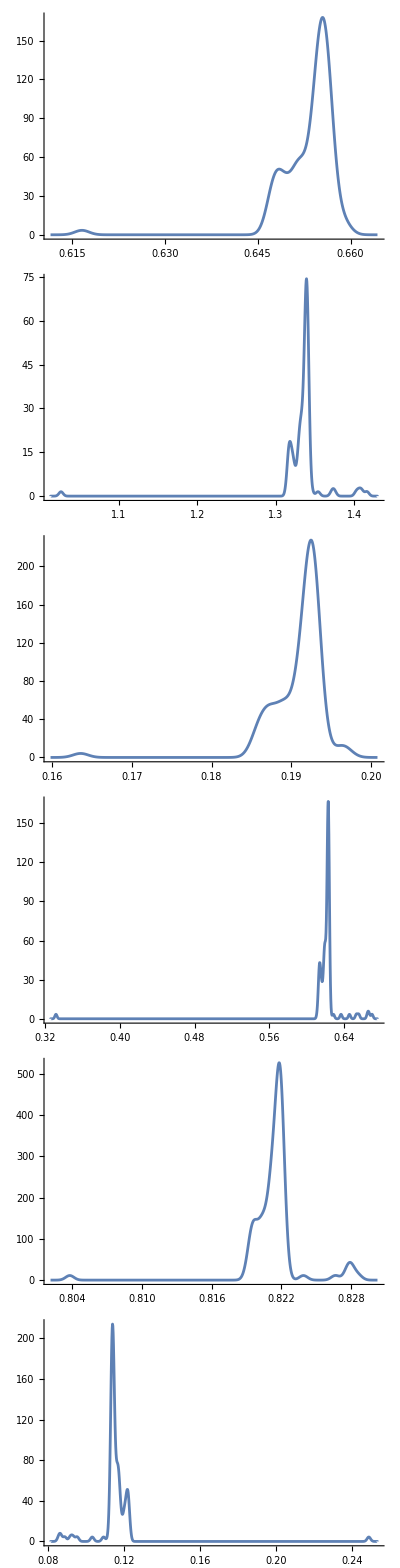

```mathematica
SmoothHistogram[#]&/@{μes1,μes2,σes1,σes2,aes1,aes2}//TableForm
```